## Matrix Element calculation

```mathematica
nmax = 15;η = 0.2; τ = 1/(1.84 10^6)
```

5.43478×10^-7

```mathematica
LaguerreL[r,s,t] //Expand
```

LaguerreL[r,s,t]

```mathematica
Min[1,2]
```

1

```mathematica
Dr[n_,nt_]:= √((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η 1)^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η 1)^2]Exp[-η^2/2];
```

```mathematica
M[n_,nt_] :=NIntegrate[Sin[θ]/2 Abs[Sum[√((Min[n,m]!)/((Min[n,m]+Abs[m-n])!))(ⅈ η Cos[θ] )^Abs[m-n] LaguerreL[Min[n,m],Abs[m-n],(η Cos[θ])^2]Exp[-(η Cos[θ])^2/2] Dr[m,nt],{m,1,nmax+1}]]^2,{θ,0, Pi}]
```

```mathematica
Dr[0,0]
```

0.980199+0. ⅈ

```mathematica
M [10,11]
```

0.219046+0. ⅈ

```mathematica
DrMat = Table[Dr[n,nt],{n,1,nmax  + 1},{nt,1,nmax + 1}] ;
```

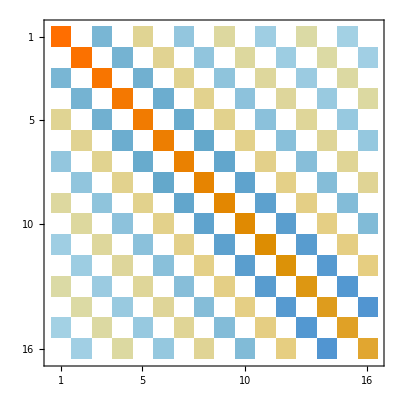

```mathematica
MatrixPlot[DrMat]
```

```mathematica
Mat = Table[M[n,nt],{n,1,nmax + 1},{nt,1,nmax +1}]
```

{{0.662351,0.236053,0.0295404,0.00215031,0.000109136,4.23447×10^-6,1.32739×10^-7,3.48739×10^-9,7.88189×10^-11,1.56253×10^-12,2.75816×10^-14,4.38733×10^-16,6.35043×10^-18,8.43212×10^-20,1.0341×10^-21,1.17816×10^-23},{0.236053,0.408022,0.291454,0.0524734,0.00493736,0.000306346,0.0000140315,5.06793×10^-7,1.50691×10^-8,3.80168×10^-10,8.32055×10^-12,1.60703×10^-13,2.77614×10^-15,4.33645×10^-17,6.18025×10^-19,8.09714×10^-21},{0.0295404,0.291454,0.265069,0.325564,0.0781276,0.00908794,0.000669305,0.000035433,1.45127×10^-6,4.82324×10^-8,1.34465×10^-9,3.22226×10^-11,6.7622×10^-13,1.26114×10^-14,2.11509×10^-16,3.22114×10^-18},{0.00215031,0.0524734,0.325564,0.160578,0.338755,0.104501,0.0146256,0.00125291,0.0000754798,3.46278×10^-6,1.27351×10^-7,3.89102×10^-9,1.01384×10^-10,2.29817×10^-12,4.60362×10^-14,8.25298×10^-16},{0.000109136,0.00493736,0.0781276,0.338755,0.0879749,0.336111,0.13022,0.0215039,0.00211005,0.000142891,7.2698×10^-6,2.93429×10^-7,9.75757×10^-9,2.74811×10^-10,6.69439×10^-12,1.43404×10^-13},{4.23447×10^-6,0.000306346,0.00908794,0.104501,0.336111,0.0407768,0.3218,0.154243,0.0296176,0.00328904,0.000247907,0.0000138728,6.10299×10^-7,2.19581×10^-8,6.65053×10^-10,1.73346×10^-11},{1.32739×10^-7,0.0000140315,0.000669305,0.0146256,0.13022,0.3218,0.0134952,0.29928,0.175816,0.0388191,0.00483189,0.000402083,0.0000245788,1.1716×10^-6,4.53759×10^-8,1.47175×10^-9},{3.48739×10^-9,5.06793×10^-7,0.000035433,0.00125291,0.0215039,0.154243,0.29928,0.00150561,0.271391,0.194422,0.0489306,0.00677303,0.000618034,0.0000410286,2.10826×10^-6,8.75554×10^-8},{7.88189×10^-11,1.50691×10^-8,1.45127×10^-6,0.0000754798,0.00211005,0.0296176,0.175816,0.271391,0.000939919,0.240434,0.209742,0.0597556,0.00913852,0.000909162,0.0000652086,3.60091×10^-6},{1.56253×10^-12,3.80168×10^-10,4.82324×10^-8,3.46278×10^-6,0.000142891,0.00328904,0.0388191,0.194422,0.240434,0.00858991,0.208249,0.221622,0.0710879,0.011946,0.0012889,0.0000997579},{2.75816×10^-14,8.32055×10^-12,1.34465×10^-9,1.27351×10^-7,7.2698×10^-6,0.000247907,0.00483189,0.0489306,0.209742,0.208249,0.0218209,0.176281,0.230034,0.0827295,0.0151876,0.00178379},{4.38733×10^-16,1.60703×10^-13,3.22226×10^-11,3.89102×10^-9,2.93429×10^-7,0.0000138728,0.000402083,0.00677303,0.0597556,0.221622,0.176281,0.0384927,0.145612,0.235212,0.0941242,0.0192176},{6.35043×10^-18,2.77614×10^-15,6.7622×10^-13,1.01384×10^-10,9.75757×10^-9,6.10299×10^-7,0.0000245788,0.000618034,0.00913852,0.0710879,0.230034,0.145612,0.0569914,0.117799,0.233478,0.110969},{8.43212×10^-20,4.33645×10^-17,1.26114×10^-14,2.29817×10^-12,2.74811×10^-10,2.19581×10^-8,1.1716×10^-6,0.0000410286,0.000909162,0.011946,0.0827295,0.235212,0.117799,0.0729682,0.0808674,0.273476},{1.0341×10^-21,6.18025×10^-19,2.11509×10^-16,4.60362×10^-14,6.69439×10^-12,6.65053×10^-10,4.53759×10^-8,2.10826×10^-6,0.0000652086,0.0012889,0.0151876,0.0941242,0.233478,0.0808674,0.13665,0.154369},{1.17816×10^-23,8.09714×10^-21,3.22114×10^-18,8.25298×10^-16,1.43404×10^-13,1.73346×10^-11,1.47175×10^-9,8.75554×10^-8,3.60091×10^-6,0.0000997579,0.00178379,0.0192176,0.110969,0.273476,0.154369,0.00511883}}

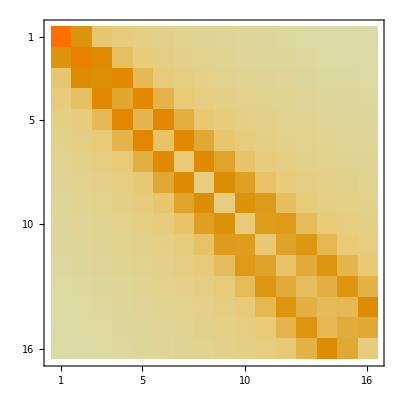

```mathematica
MatrixPlot[Mat]
```

```mathematica
Table[ Sum[Mat[[j,m]],{m,1,11}],{j,1,16}]
```

{0.980684,0.999521,0.999992,1.,1.,1.,0.999999,0.999954,0.998056,0.958896,0.661589,0.331461,0.0468494,0.00307233,0.000119261,3.13364×10^-6}

```mathematica
{0.9500066076371911+0. ⅈ,0.9981858353884894+0. ⅈ,0.9999252554603134+0. ⅈ,0.9999975389684228+0. ⅈ,0.9999999137599004+0. ⅈ,0.9999989443099998+0. ⅈ,0.9999639056062806+0. ⅈ,0.9991850718498525+0. ⅈ,0.9869398839062721+0. ⅈ,0.8466419397926749+0. ⅈ,0.11540074126484189+0. ⅈ}
Table[ Sum[M[j,m],{m,1,40}],{j,1,40}]
```

{0.950007+0. ⅈ,0.998186+0. ⅈ,0.999925+0. ⅈ,0.999998+0. ⅈ,1.+0. ⅈ,0.999999+0. ⅈ,0.999964+0. ⅈ,0.999185+0. ⅈ,0.98694+0. ⅈ,0.846642+0. ⅈ,0.115401+0. ⅈ}

{0.980684,0.999521,0.999992,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999894,0.993787,0.84998,0.149262,0.00692783,0.000149055,1.88655×10^-6,1.59863×10^-8,9.83276×10^-11,4.63835×10^-13,1.74623×10^-15,5.40682×10^-18,1.40948×10^-20,3.15211×10^-23,6.1407×10^-26,1.05545×10^-28,1.61778×10^-31,2.23173×10^-34,2.79275×10^-37,3.1921×10^-40,3.3527×10^-43,3.25314×10^-46,2.92995×10^-49,2.45986×10^-52,1.93247×10^-55,1.42548×10^-58,9.90425×10^-62}

```mathematica
Adiabatic elimination of state 2
```

```mathematica
α = 0.6;
```

```mathematica
Eigenvalues[Mat]
```

{0.976214,0.897995,0.77029,0.605649,0.4216,-0.396012,-0.386373,-0.342232,-0.329749,-0.238988,0.234944,-0.227032,0.114543,-0.102563,-0.0745253,0.0575847}

```mathematica
MatEl2 = Mat.Inverse[IdentityMatrix[nmax+1]-(1-α)*Mat]
```

{{0.954779,0.404881,0.102856,0.0279754,0.00872632,0.00299201,0.00110513,0.000434009,0.0001794,0.0000774668,0.00003474,0.0000161027,7.68345×10^-6,3.75126×10^-6,1.86626×10^-6,1.02066×10^-6},{0.404881,0.596805,0.430603,0.136481,0.0417737,0.0143207,0.00529434,0.00207865,0.00085924,0.000371034,0.000166389,0.0000771251,0.0000368004,0.0000179669,8.93855×10^-6,4.88854×10^-6},{0.102856,0.430603,0.4247,0.443555,0.166871,0.0557615,0.0205896,0.00809835,0.00334597,0.00144486,0.000647971,0.000300345,0.00014331,0.0000699677,0.000034809,0.0000190372},{0.0279754,0.136481,0.443555,0.309128,0.439877,0.191954,0.0686285,0.0269025,0.011151,0.0048115,0.0021577,0.00100023,0.000477246,0.000233003,0.00011592,0.0000633972},{0.00872632,0.0417737,0.166871,0.439877,0.230025,0.42576,0.212954,0.0803547,0.0330687,0.0143454,0.00642589,0.00297823,0.00142132,0.00069389,0.000345208,0.000188798},{0.00299201,0.0143207,0.0557615,0.191954,0.42576,0.176589,0.4047,0.230768,0.091057,0.0389768,0.0176064,0.00814833,0.00388663,0.0018982,0.000944295,0.000516423},{0.00110513,0.00529434,0.0205896,0.0686285,0.212954,0.4047,0.142163,0.378845,0.245989,0.100908,0.0445578,0.0208786,0.0099436,0.00485062,0.00241464,0.00132047},{0.000434009,0.00207865,0.00809835,0.0269025,0.0803547,0.230768,0.378845,0.122268,0.349666,0.258968,0.110102,0.0497657,0.0241138,0.011751,0.00583576,0.00319472},{0.0001794,0.00085924,0.00334597,0.011151,0.0330687,0.091057,0.245989,0.349666,0.11365,0.318295,0.269862,0.118836,0.0545608,0.0271961,0.0135151,0.00736897},{0.0000774668,0.000371034,0.00144486,0.0048115,0.0143454,0.0389768,0.100908,0.258968,0.318295,0.113768,0.28569,0.278667,0.127273,0.0587611,0.030025,0.0164156},{0.00003474,0.000166389,0.000647971,0.0021577,0.00642589,0.0176064,0.0445578,0.110102,0.269862,0.28569,0.120493,0.252694,0.285217,0.135202,0.0621688,0.0351848},{0.0000161027,0.0000771251,0.000300345,0.00100023,0.00297823,0.00814833,0.0208786,0.0497657,0.118836,0.278667,0.252694,0.131903,0.220004,0.288502,0.142824,0.0707118},{7.68345×10^-6,0.0000368004,0.00014331,0.000477246,0.00142132,0.00388663,0.0099436,0.0241138,0.0545608,0.127273,0.285217,0.220004,0.146026,0.187547,0.288809,0.158024},{3.75126×10^-6,0.0000179669,0.0000699677,0.000233003,0.00069389,0.0018982,0.00485062,0.011751,0.0271961,0.0587611,0.135202,0.288502,0.187547,0.156877,0.142124,0.31069},{1.86626×10^-6,8.93855×10^-6,0.000034809,0.00011592,0.000345208,0.000944295,0.00241464,0.00583576,0.0135151,0.030025,0.0621688,0.142824,0.288809,0.142124,0.196881,0.196438},{1.02066×10^-6,4.88854×10^-6,0.0000190372,0.0000633972,0.000188798,0.000516423,0.00132047,0.00319472,0.00736897,0.0164156,0.0351848,0.0707118,0.158024,0.31069,0.196438,0.0589393}}

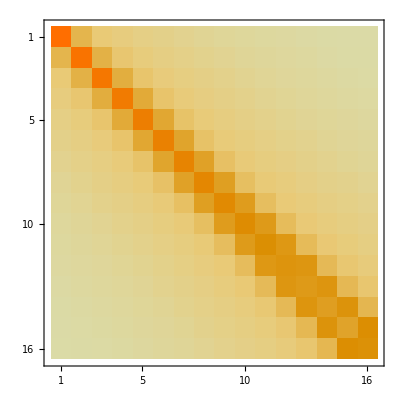

```mathematica
MatrixPlot[MatEl2]
```

```mathematica
Table[ Sum[MatEl2 [[j,m]],{m,1,11}],{j,1,16}]
```

{1.50404,1.63363,1.65847,1.66262,1.66018,1.65049,1.62573,1.56849,1.43712,1.13766,0.857744,0.733362,0.507081,0.240678,0.11541,0.0642781}